```mathematica
ClearAll["Global`*"] (* clear variables *)

(* switch off message that solar panels cannot be lower than 0 degrees *)
Off[FindMinimum::reged];
Off[FindMaximum::reged];

(* Adjusting the solar panels x times a day
The times are evenly spread over the time the sun is up *)
year = 2016;

(* parameters are forced numeric, so findMaximum in dayangle works better *)
angle[i_?NumericQ,a_?NumericQ,d_]:= ( (* params: index of sunPositions table, solar panel angle in degrees, date, returns misalignment with the sun in radians *)
sunPos = sunPositions[[i]]; (* lookup sun position *)

(* remove degree unit, then convert to radians *)
gammaS= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
gammaS = gammaS - Pi;
thetaS= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
gammaP = -22 * Pi/180; (* Solar panels azimuth *)
thetaP = a * Pi/180; (* Solar panels angle with horizontal *)
ArcCos[Cos[gammaP-gammaS] Cos[thetaS] Sin[thetaP]+Cos[thetaP] Sin[thetaS]]
)


(* parameters from urban visibility haze model *)
directPower[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
(* here comes the magik formula from http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 for a clear day *)
n= QuantityMagnitude[Quantity[d - DateObject[{2016,1,1}]]]; (* day of year *)
i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.2538 - 0.0063 36;
aOne = 0.7678 + 0.001 6.5^2;
k = 0.249 + 0.081 2.5^2;
If[Cos[theta]<0,
0,
i (aZero + aOne E^(-k/Cos[theta])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
] 
)

sumOverInterval:=Function[ (* params: solar panel angle in degrees, date, start index, end index
returns sum of solar power over the day at every hour in the given interval *)
(* take sum of every index, hence steps of one *)
Sum[directPower[i,#1,#2],{i,#3,#4,1}]
]

angleInterval := Function[ (* params: date, start index, end index, returns optimal angle in this interval *)
(* Find for which angle of the solar panels this value is maximal,starting at 0 *)
res = FindMaximum[sumOverInterval[x,#1,#2,#3],{x,0,0,90}, AccuracyGoal->5];
{res[[1]],x /. res[[2]]}
]

dayAngles := Function[ (* params: date, number of adjustment times per day ≥ 1. returns List with optimal angles and power received with that angle over that interval, for how many adjustment times were specified *)
position = GeoPosition[{51.546545,4.411744}];
sunrise = Sunrise[position,#1];
TimeZoneConvert[sunrise,2];
sunriseHour = DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60;
sunset = Sunset[position,#1];
TimeZoneConvert[sunset,2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;

(* generate sun position table, so angle[] can access it every time *)
sunPositions = Table[
 SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[#1,{h/100}]],
{h,sunriseHour*100,sunsetHour*100,10} (* steps of .1 hours, .02 doesn't help *)
];

l = Length[sunPositions];
Table[ (* calculates indices of start and end of the interval *)
angleInterval[#1,1+Round[l*i/#2],Round[l*(i+1)/#2]]
,{i,0,#2-1}]
]

(*twoAnglesOptimal[] := (

)*)

dayPower[t_] := ( (* total of power *)
sum = 0;
For[i=1,i<Length[t]+1,i++,
sum += t[[i]][[1]];
];
sum (* Total of W/m^1 received *)
)

dayPowerTable[t_] := ( (* list of power received for each angle-period *)
Table[
t[[i]][[1]],
{i,1,Length[t]}
]
)

dayAnglesTable[t_] := (
(* make list of angles *)
Table[
t[[i]][[2]],
{i,1,Length[t]}
]
)

(* find div(ision) where total W/m^m is biggest *)
totalPower[d_,v_] := ( (* params: date, division as index of sunPositions. returns total power of day, and list with two angles *)
first = angleInterval[d,1,v];
second = angleInterval[d,v+1,l];
total = first[[1]] + second[[1]];
angles = {first[[2]],second[[2]]};
{total,angles}
)

 (*  NOTE for a preciser adjustment time, change step size where noted. will increase running time by as much steps are added times around three seconds *)
twoAnglesOptimal[d_] := (  (* params: date; returns in a list the date/time at which to change the angle of solar panels (besides before sunrise) to get optimal power, then the two angles of the day, then the percent increase of power compared to one setting for the whole day, then the percent increase compared to one setting if you would adjust fourteen times a day, spread evenly over the day *)
(* for two angles per day, find optimal time of angle change *)

(* some initialisation of the sunposition table *)
position = GeoPosition[{51.546545,4.411744}];
sunrise = Sunrise[position,d];
TimeZoneConvert[sunrise,2];
sunriseHour = DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60;
sunset = Sunset[position,d];
TimeZoneConvert[sunset,2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
(* generate sun position table, so angle[] can access it every time *)
sunPositions = Table[
 SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[d,{h/100}]],
{h,sunriseHour*100,sunsetHour*100,10} (* steps of .1 hours, .02 doesn't help *)
];
l = Length[sunPositions];

(* steps of about one per hour is l/14 *)
(*DiscretePlot[totalPower[d,v],{v,Round[l/2],l,Round[l/12]},ImageSize -> Large]*)
t = Table[{v,totalPower[d,v]},{v,Round[l/2],Round[4 l/5],Round[l/14]}];
max = Max[t]; (* total power over the day with this setting *)
index = t[[Position[t,Max[t]][[1]][[1]]]][[1]] ;
angles = t[[Position[t,Max[t]][[1]][[1]]]][[2]][[2]] ;
(* brackets! gives index around which the highest total resides *)
(* index back to time *)
hour =(index/l)*(sunsetHour - sunriseHour)+sunriseHour ; (* the hour at which to set the solar panels second time *)
(* find percentage increase in power *)
onePower = dayAngles[d,1][[1]][[1]]; (* find power for one time *)
(* compare with percent increase in power if you'd adjust 10 times a day (not optimised) *)
tenPower= dayPower[dayAngles[d,14]];
(* return values *)
{DateObject[d,{IntegerPart[hour],Round[FractionalPart[hour]*60]}],angles,(max - onePower)/onePower * 100,(tenPower - onePower)/onePower * 100}
)

dayAngles[DateObject[{2016,7,18}],1]; (* make sure to initialize sunPositions table *)

(******************************* END OF FUNCTIONS ***************************)
(* optimizing by angle only! *)
(*dayAngles[DateObject[{2016,8,17}],2] //Timing*)
(*res = dayAngles[DateObject[{2016,8,19}],14]
ListPlot[Table[res[[i]][[2]] ,{i,1,Length[res]}]]*)

(* percentages *)
(*t = Table[
dayPower[dayAngles[DateObject[{2016,8,17}],x]],
{x,1,10}
]
(* relative to first *)
Table[
(t[[i]]-t[[1]])/t[[1]],
{i,2,Length[t]}
]
(* relative to previous *)
Table[
(t[[i]]-t[[i-1]])/t[[i-1]],
{i,2,Length[t]}
]*)

(*DiscretePlot[ dayPower[dayAngles[DateObject[{2016,7,18}],x]],{x,1,20,1}] //Timing*)


twoAnglesOptimal[DateObject[{2016,8,17}]] //Timing
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{60.4688,{Wed 17 Aug 2016 15:44GMT+2.,{41.8088,0.},7.50911,8.61506}}

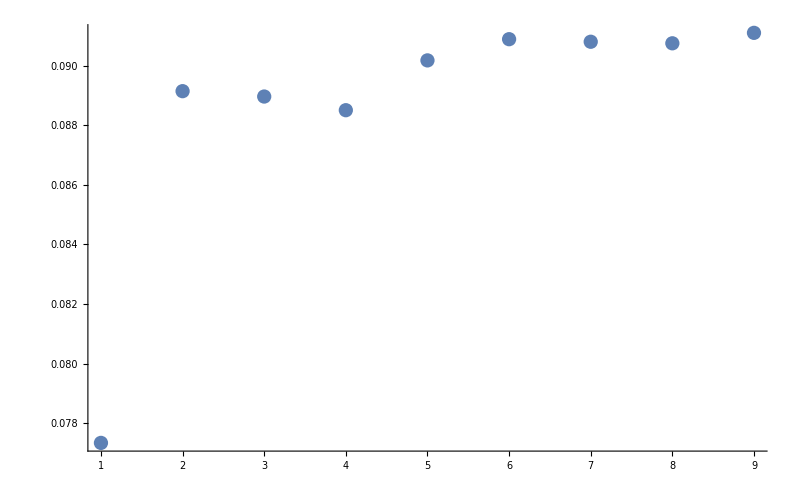
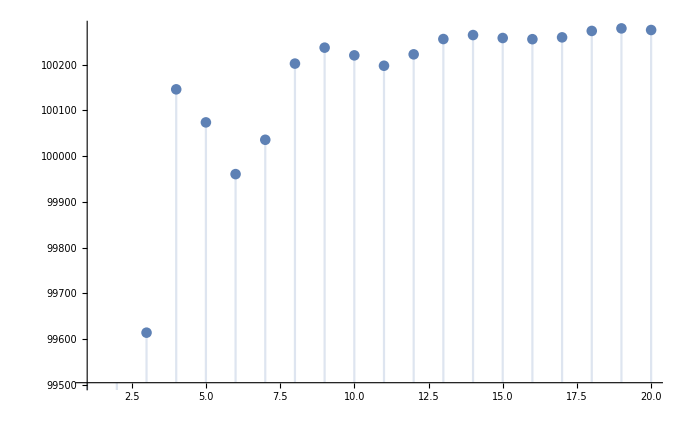
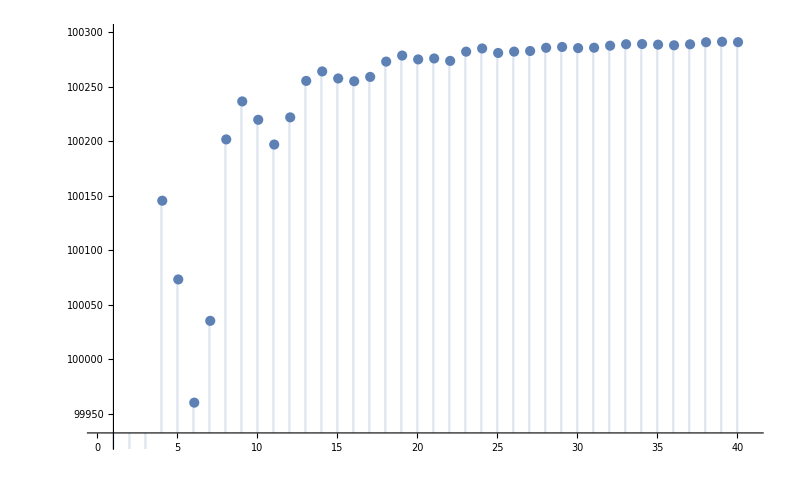
```mathematica
(* Example output of twoAnglesOptimal *)
{DateObject[{2016,8,17},TimeObject[{15,44},TimeZone->2.],TimeZone->2.],{41.80,0},7.5,8.6}

(* percentages change, first relative to the first, then to the previous *)
{0,0.0214891,0.0269413,0.0262005,0.0250416,0.025811,0.0275178,0.0278751,0.0277023}
{0,0.0214891,0.00533747,-0.000721313,-0.00112938,0.000750613,0.00166387,0.000347719,-0.000168099}

(* with -22 azimuth: *)
{0.0773427,0.0891427,0.0889624,0.088504,0.090175,0.0908864,0.0908002,0.0907483,0.0910989}
{0.0773427,0.0109529,-0.00016553,-0.000420986,0.00153513,0.000652584,-0.0000789884,-0.0000475611,0.000321402}
-Graphics--Graphics--Graphics-
```

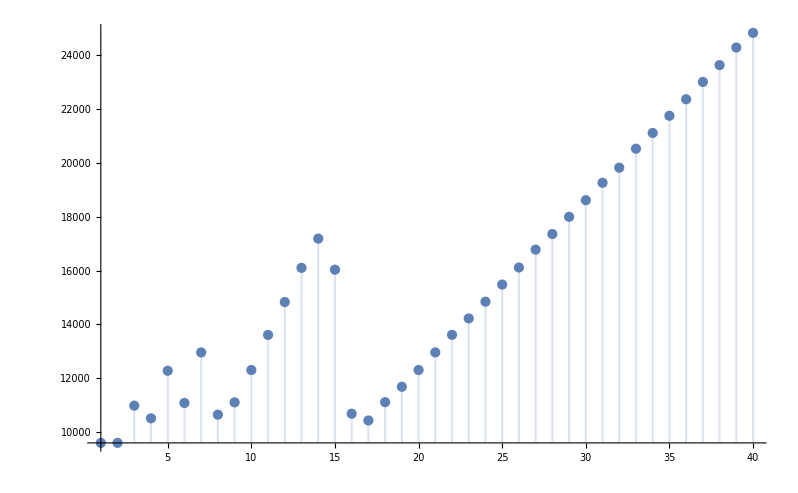
```mathematica
old -Graphics-
```